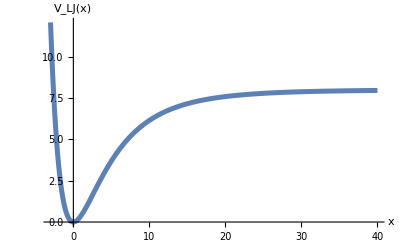

```mathematica
Plot[1/2 16((6/(x/4+6))^12-2(6/(x/4+6))^6+1),{x,-3,40},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_LJ(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

```mathematica
s=Table[DiscreteDelta[j-i-1] √(j-1),{i,16},{j,16}];
```

```mathematica
Xosc:=1/(√2)(s+Transpose[s])
Posc:= ⅈ N[1/(√2)(-s+Transpose[s])]

Hquadraticosc := .5 Posc.Posc + .5 Xosc.Xosc
Reverse[N[Eigenvalues[Hquadraticosc]]]
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5}

```mathematica
HamiltonianLJ:= .5 Posc.Posc + 8 (MatrixPower[(Xosc/4 + 6 IdentityMatrix[16])/6,-12]- 2MatrixPower[(Xosc/4 + 6 IdentityMatrix[16])/6,-6]+IdentityMatrix[16])
```

```mathematica
Sort[Reverse[N[Eigenvalues[ HamiltonianLJ]]]]
```

{0.490921,1.41323,2.26027,3.03476,3.74343,4.43836,5.21618,6.15515,7.24127,8.42684,10.0142,11.242,13.0947,18.4955,30.8104,59.0852}

```mathematica
HamiltonianLJ=Chop[HamiltonianLJ];
SetDirectory[NotebookDirectory[]];
saveHam[ham_]:=Export["./"<>"HamiltonianLJ.txt",ham,"Table"]

saveHam[HamiltonianLJ];
```